```mathematica
q1 =l  BesselI[nu-1, √(l x)] - √(l x)BesselI[nu, √(l x)]
```

l BesselI[-1+nu,√(l x)]-√(l x) BesselI[nu,√(l x)]

```mathematica
q2 = q1 /. x->  l +2nu-1 + eps
```

l BesselI[-1+nu,√(l (-1+eps+l+2 nu))]-√(l (-1+eps+l+2 nu)) BesselI[nu,√(l (-1+eps+l+2 nu))]

```mathematica
FullSimplify[Series[q2, {eps, 0, 2}]]
```

(l BesselI[-1+nu,√(l (-1+l+2 nu))]-√(l (-1+l+2 nu)) BesselI[nu,√(l (-1+l+2 nu))])+1/2 l (-((l+nu) BesselI[-1+nu,√(l (-1+l+2 nu))])/(-1+l+2 nu)+((-1+l+nu) BesselI[nu,√(l (-1+l+2 nu))])/(√(l (-1+l+2 nu)))) eps+((l (3-l+l^2+2 (-2+l) nu+nu^2) BesselI[-1+nu,√(l (-1+l+2 nu))]-√(l (-1+l+2 nu)) (-1+l+l^2+2 l nu+nu^2) BesselI[nu,√(l (-1+l+2 nu))]) eps^2)/(8 (-1+l+2 nu)^2)+O[eps]^3

```mathematica
q3 = q1/. x -> l - 2 nu
```

l BesselI[-1+nu,√(l (l-2 nu))]-√(l (l-2 nu)) BesselI[nu,√(l (l-2 nu))]

```mathematica
N[q3/. {l-> 17, nu-> -1/2}]
```

-5.52425×10^6

```mathematica
Solve[q3==0, x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[l BesselI[-1+nu,√(l x)]-√(l x) BesselI[nu,√(l x)]==0,x]

```mathematica
q1 =l  BesselI[nu-1, √(l g)] - √(l g)BesselI[nu, √(l g)];
Block[{l=10., nu=4.},
{FindMinimum[q1^2, {g, l+2nu - 1.}, WorkingPrecision->100], l +2nu -1,-1+l+(-1/2+nu)/l+2 nu,(-3+4 l^3-4 (-2+nu) nu+l (-2+4 nu)+l^2 (-4+8 nu))/(4 l^2),(-57+200 nu+4 (l (-6+l (-3+2 l (-1+2 (-1+l) l)))+l (19+4 l (2+l+2 l^2)) nu-2 (27+2 l (4+l)) nu^2+4 (6+l) nu^3-4 nu^4))/(16 l^4)} 
(*LogPlot[q1^2, {x, l+2 nu -1.5, l + 2nu + 1.5}]*)
]
```

{{0,{g→17.2768792716810814931734727958710373737335362064728176378953755407681678716359802918675963838532921}},17.,17.35,17.2625,17.2758}

```mathematica
FindMinimum[q1^2, {x, l+2nu - 1.}, WorkingPrecision->100]
```

FindMinimum[q1^2,{x,l+2 nu-1.},WorkingPrecision→100]

```mathematica
N[q1/.{l->17, nu->, x->2}]
```

195.287

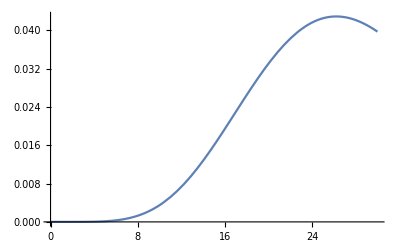

```mathematica
Plot[PDF[NoncentralChiSquareDistribution[12, 17]][x], {x, 0, 30}]
```

```mathematica
Simplify[Solve[((t/x - 1/(2 nu/t+1/(2(nu+1)/t+1/(2 (nu+2)/t))))/.t-> √(l x) )== 0, x]]
```

{{x→-(2 (2+3 nu+nu^2-l (1+nu)+√((1+nu) (l^2 (1+nu)-2 l (2+nu)+(1+nu) (2+nu)^2))))/l},{x→(2 (-2+l-3 nu+l nu-nu^2+√((1+nu) (l^2 (1+nu)-2 l (2+nu)+(1+nu) (2+nu)^2))))/l}}

```mathematica
Integrate[(2nu+l)/(-l(2nu + l -2)), l]
```

-(nu Log[l]-Log[2-l-2 nu])/(-1+nu)

```mathematica
Simplify[D[-(nu Log[l]-Log[-2+l+2 nu])/(-1+nu), l]]
```

-(l+2 nu)/(l (-2+l+2 nu))

```mathematica
AsymptoticDSolve[(x[l] + l x'[l])(x[l] -l -f)+l x'[l] -x[l] == 0, x, l]]
```

$Aborted

```mathematica
AsymptoticDSolveValue[(t-f) x'[t] (x[t] - t +1) +x[t](x[t] - t -1)==0, x, t,{f,0, 1}]
```

AsymptoticDSolveValue[x[t] (-1-t+x[t])+(-f+t) (1-t+x[t]) x'[t]==0,x,t,{f,0,1}]

```mathematica
With[{, ,
(*CoefficientList[Series[(ξ-1)ξ D[x, ξ](x ξ + ξ- f) + x(x ξ - ξ - f), {ξ, 0, 2}], ζ]*)

]
```

-f x+(-1+x) x ξ+O[ξ]^4

```mathematica
y=f+f t+t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+d t^6
FullSimplify[(y/t /. t-> f/l) /. f -> 2nu -1 /. d->0]
n = Length[CoefficientList[y, t]]-1
m = -t D[y, t] (y - f t -f +t)+2y ( y-f t - f )
FullSimplify[m]
s = SeriesCoefficient[m, {t, 0, n}]
res =Solve[s==0,d ]
y = y/. res
```

f+f t+t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+d t^6

(-57+200 nu+4 (l (-6+l (-3+2 l (-1+2 (-1+l) l)))+l (19+4 l (2+l+2 l^2)) nu-2 (27+2 l (4+l)) nu^2+4 (6+l) nu^3-4 nu^4))/(16 l^4)

6

-t (f+t+(3 (2-f) t^2)/(4 f)+((6-5 f+f^2) t^3)/(2 f^2)+(5 (24-24 f+8 f^2-f^3) t^4)/(16 f^3)+6 d t^5) (t+t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+d t^6)+2 (t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+d t^6) (f+f t+t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+d t^6)

1/(256 f^6)t^6 (16 f^3 (-120+f (128+f (-50+f (10+(-1+32 d) f))))+8 f^3 (-108+f (120+f (-45+6 f+32 d (-6+f) f))) t-8 f^2 (132+f (-204+f (117+f (-30+(3+64 d) f)))) t^2+10 (-2+f) f (72+f (-96+f (48+f (-11+f+32 d f)))) t^3-3 (-2+f) (-288+f (432+f (-264+f (84+f (-14+64 d (-3+f)+f))))) t^4+112 d (-2+f) f^3 (12+(-6+f) f) t^5-1024 d^2 f^6 t^6)

(-120+128 f-50 f^2+10 f^3-f^4+32 d f^4)/(16 f^3)

{{d→(120-128 f+50 f^2-10 f^3+f^4)/(32 f^4)}}

{f+f t+t^2/2+((2-f) t^3)/(4 f)+((6-5 f+f^2) t^4)/(8 f^2)+((24-24 f+8 f^2-f^3) t^5)/(16 f^3)+((120-128 f+50 f^2-10 f^3+f^4) t^6)/(32 f^4)}

```mathematica
f = 2nu -1
```

f+f t+t^2/2+d t^3

(2 d (1-2 nu)^2+l (-1+2 nu+2 l (-1+l+2 nu)))/(2 l^2)

3

-t (f+t+3 d t^2) (t+t^2/2+d t^3)+2 (t^2/2+d t^3) (f+f t+t^2/2+d t^3)

1/2 t^3 (-2+f+2 d f (2+t)-d t (6+t+2 d t^2))

-1+f/2+2 d f

{{d→(2-f)/(4 f)}}

{f+f t+t^2/2+((2-f) t^3)/(4 f)}

```mathematica
((2-f) t^3)/(4 f)
```

```mathematica
FullSimplify[m, ξ]
```

0

```mathematica
x=1+f+(f (1+f) ξ)/(-1+f)/.ξ-> f/l
FullSimplify[l D[x, l] (x - f - l +1)+x(x-f - l -1)]
```

1+f+(f^2 (1+f))/((-1+f) l)

((1+f) (f-l) (f+l))/l

```mathematica
ξ+(2 ξ^2)/f-((-3+f) ξ^3)/f^2+(2 (6-4 f+f^2) ξ^4)/(3 f^3)+((30-23 f+14 f^2-3 f^3) ξ^5)/(6 f^4)+((90-39 f+46 f^2-31 f^3+6 f^4) ξ^6)/(15 f^5)/.ξ-> f/l /.f -> 2 ν +1
```

```mathematica
(2 (1+2 ν))/l^2+(1+2 ν)/l-((-2+2 ν) (1+2 ν))/l^3+(2 (1+2 ν) (6-4 (1+2 ν)+(1+2 ν)^2))/(3 l^4)+((1+2 ν) (30-23 (1+2 ν)+14 (1+2 ν)^2-3 (1+2 ν)^3))/(6 l^5)+((1+2 ν) (90-39 (1+2 ν)+46 (1+2 ν)^2-31 (1+2 ν)^3+6 (1+2 ν)^4))/(15 l^6)/. {l-> 12, ν->2}//N
```

0.481827

```mathematica
AsymptoticDSolveValue[(t-f) g'[t] (g[t] - t +1) +g[t](g[t] - t -1)==0, g, t,{f,0, 1}]
```

$Aborted